```mathematica
g=0.02;
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[HBdG[0.,0.,g]]]]];
```

```mathematica
n=2Nx;
e[[n]]
ψeu0=Table[ψ[[n,i]],{i,1,2Nx,2}];
ψed0=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu0=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd0=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];
```

-0.000270072

```mathematica
n=2Nx+1;
e[[n]]
ψeu1=Table[ψ[[n,i]],{i,1,2Nx,2}];
ψed1=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu1=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd1=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];
```

0.000270072

```mathematica
n=2Nx+2;
e[[n]]
ψeu2=Table[ψ[[n,i]],{i,1,2Nx,2}];
ψed2=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu2=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd2=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];
```

0.0491404

```mathematica
n=2Nx+3;
e[[n]]
ψeu3=Table[ψ[[n,i]],{i,1,2Nx,2}];
ψed3=Table[ψ[[n,i]],{i,2,2Nx,2}];
ψhu3=Table[ψ[[n,i]],{i,2Nx+1,4Nx,2}];
ψhd3=Table[ψ[[n,i]],{i,2Nx+2,4Nx,2}];
```

0.0581619

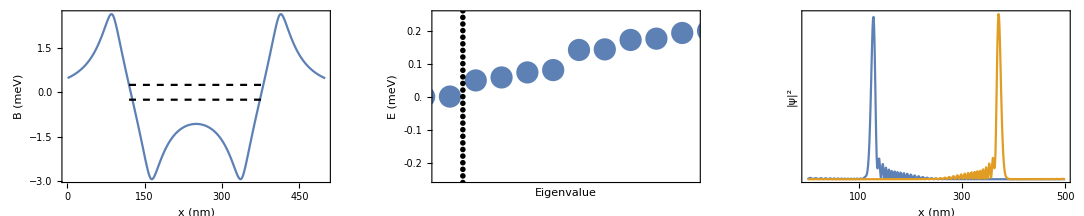

```mathematica
line=Table[{1001.5+0.000001*i,-0.3+0.02*i},{i,0,30}];
GraphicsRow[{ListPlot[{g*MagΔ,{{Nxn,Δ},{500-Nxn,Δ}},{{Nxn,-Δ},{500-Nxn,-Δ}}},PlotRange->All,Joined->True,Frame->True,FrameLabel->{{"B (meV)",None},{"x (nm)",None}},LabelStyle->{Black,20},PlotStyle->{Back,{Black,Dashed},{Black,Dashed}}],ListPlot[{e,line},PlotRange->{{1000.5,1010.5},{-Δ,Δ}},PlotStyle->{PointSize[0.04],{Black,PointSize[0.01]}},Frame->True,FrameLabel->{{"E (meV)",None},{"Eigenvalue",None}},LabelStyle->{Black,20},FrameTicks->{{{-0.2,-0.1,0.0,0.1,0.2},None},{None,None}}],ListPlot[{Abs[ψeu1-ψhu1]^2+Abs[ψed1-ψhd1]^2+Abs[ψeu0-ψhu0]^2+Abs[ψed0-ψhd0]^2,Abs[ψeu1+ψhu1]^2+Abs[ψed1+ψhd1]^2+Abs[ψeu0+ψhu0]^2+Abs[ψed0+ψhd0]^2},Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"|ψ|^2",None},{"x (nm)",None}},LabelStyle->{Black,20},FrameTicks->{{None,None},{{100,200,300,400,500},None}}]}]
```

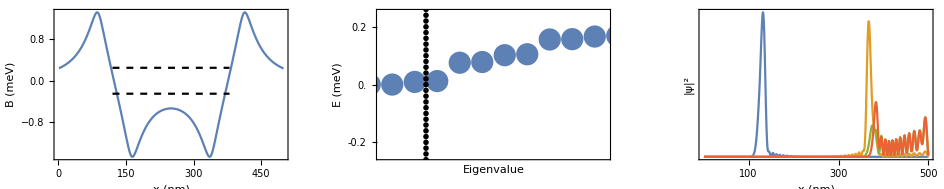

```mathematica
line=Table[{1002.5+0.000001*i,-0.3+0.02*i},{i,0,30}];
GraphicsRow[{ListPlot[{g*MagΔ,{{Nxn,Δ},{500-Nxn,Δ}},{{Nxn,-Δ},{500-Nxn,-Δ}}},PlotRange->All,Joined->True,Frame->True,FrameLabel->{{"B (meV)",None},{"x (nm)",None}},LabelStyle->{Black,20},PlotStyle->{Back,{Black,Dashed},{Black,Dashed}}],ListPlot[{e,line},PlotRange->{{1000.5,1010.5},{-Δ,Δ}},PlotStyle->{PointSize[0.04],{Black,PointSize[0.01]}},Frame->True,FrameLabel->{{"E (meV)",None},{"Eigenvalue",None}},LabelStyle->{Black,20},FrameTicks->{{{-0.2,-0.1,0.0,0.1,0.2},None},{None,None}}],ListPlot[{Abs[ψeu1-ψhu1]^2+Abs[ψed1-ψhd1]^2+Abs[ψeu0-ψhu0]^2+Abs[ψed0-ψhd0]^2,Abs[ψeu1+ψhu1]^2+Abs[ψed1+ψhd1]^2+Abs[ψeu0+ψhu0]^2+Abs[ψed0+ψhd0]^2,2 Abs[ψeu2+ψhu2]^2+2 Abs[ψed2+ψhd2]^2,2 Abs[ψeu2-ψhu2]^2+2 Abs[ψed2-ψhd2]^2},Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"|ψ|^2",None},{"x (nm)",None}},LabelStyle->{Black,20},FrameTicks->{{None,None},{{100,200,300,400,500},None}}]}]
```

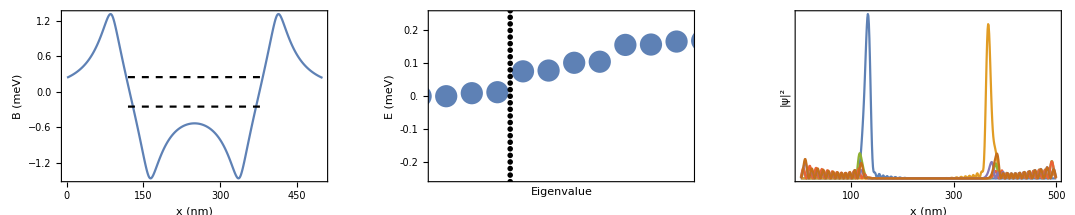

```mathematica
line=Table[{1003.5+0.000001*i,-0.3+0.02*i},{i,0,30}];
GraphicsRow[{ListPlot[{g*MagΔ,{{Nxn,Δ},{500-Nxn,Δ}},{{Nxn,-Δ},{500-Nxn,-Δ}}},PlotRange->All,Joined->True,Frame->True,FrameLabel->{{"B (meV)",None},{"x (nm)",None}},LabelStyle->{Black,20},PlotStyle->{Back,{Black,Dashed},{Black,Dashed}}],ListPlot[{e,line},PlotRange->{{1000.5,1010.5},{-Δ,Δ}},PlotStyle->{PointSize[0.04],{Black,PointSize[0.01]}},Frame->True,FrameLabel->{{"E (meV)",None},{"Eigenvalue",None}},LabelStyle->{Black,20},FrameTicks->{{{-0.2,-0.1,0.0,0.1,0.2},None},{None,None}}],ListPlot[{Abs[ψeu1-ψhu1]^2+Abs[ψed1-ψhd1]^2+Abs[ψeu0-ψhu0]^2+Abs[ψed0-ψhd0]^2,Abs[ψeu1+ψhu1]^2+Abs[ψed1+ψhd1]^2+Abs[ψeu0+ψhu0]^2+Abs[ψed0+ψhd0]^2,Abs[ψeu2+ψhu2+ψeu3+ψhu3]^2,Abs[ψeu2-ψhu2+ψeu3-ψhu3]^2,Abs[ψed2+ψhd2-ψed3-ψhd3]^2,Abs[ψed2-ψhd2-ψed3+ψhd3]^2},Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"|ψ|^2",None},{"x (nm)",None}},LabelStyle->{Black,20},FrameTicks->{{None,None},{{100,200,300,400,500},None}}]}]
```